# Introdução à Física Computacional I (2023.2)

## Aula 5: somas; séries; solução de equações diferenciais ordinárias Capítulos 2.2.11, 2.2.12 e 2.2.14

## Somas

O Mathematica lida com somas tanto de forma analítica quanto numericamente.

Somas analíticas são obtidas a partir da função Sum, cuja sintaxe é semelhante à da função Integrate:

```mathematica
(Sum[1/x^n,{n,0,6}])/.x->1(* Soma das potências de x entre 1/x^0 e 1/x^6 *)
```

7

```mathematica
Table[1/x^n,{n,0,6}](*O table gera listac*)
```

{1,1/x,1/x^2,1/x^3,1/x^4,1/x^5,1/x^6}

```mathematica
Sum[1/n^4,{n,7}] (* Soma de 1/n^4 de n=1 até n=7 *)
```

33654237761/31116960000

```mathematica
N[%]
```

1.08154

O incremento da variável de soma, que por padrão é igual a 1, pode ser controlado acrescentando um quarto elemento ao iterador:

```mathematica
Sum[1/x^n,{n,0,10,2}]
```

1+1/x^10+1/x^8+1/x^6+1/x^4+1/x^2

Somas múltiplas também podem ser efetuadas. Por exemplo, para obter ∑_(n=1)^3 ∑_(m=1)^n 1/(x^n+y^m), escrevemos

```mathematica
Sum[1/(x^n+y^m),{n,1,3},{m,1,n}]
```

1/(x+y)+1/(x^2+y)+1/(x^3+y)+1/(x^2+y^2)+1/(x^3+y^2)+1/(x^3+y^3)

O valor de uma série infinita, desde que convergente, pode ser calculado. Por exemplo, o resultado matemático célebre ∑_(n=1)^∞ 1/n^2=π^2/6 é reproduzido:

```mathematica
Sum[1/n^2,{n,1,∞}]
```

π^2/6

Um segundo exemplo: ∑_(n=1)^∞ 1/((4n+1)(4n-3))

```mathematica
Sum[1/((4*n+1)*(4*n-3)),{n,1,∞}]
```

1/4

Em alguns casos, é possível obter resultados de somas simbólicas:

```mathematica
Sum[1/(j*(j+1)),{j,1,n}]//Simplify
```

n/(1+n)

```mathematica
Sum[q^j,{j,0,n}]//Simplify
```

(-1+q^(1+n))/(-1+q)

Quando o Mathematica não consegue expressar a soma de forma exata, a saída basicamente repete a entrada. Por exemplo, no caso de ∑_(n=1)^∞ n^2/(1+2 e^n):

```mathematica
Sum[(n^2)/(1+2*Exp[n]),{n,1,∞}]
```

∑_(n=1)^∞ n^2/(1+2 ⅇ^n)

Nesse caso, é possível aproximar a soma numericamente. Seria possível utilizar a construção N[Sum[...]], mas isso faria o Mathematica primeiro tentar calcular a soma de forma exata, desperdiçando tempo. Em vez disso, podemos utilizar a função NSum:

```mathematica
NSum[(n^2)/(1+2*Exp[n]),{n,1,∞}]
```

0.943293

## Séries de potências

Representações em séries de potências de uma função f(x) em torno de x=x_0 são obtidas no Mathematica utilizando a função Series. Por exemplo, para obter a expansão até ordem u^11 da função exp(sen(u)) em torno de u=0:

```mathematica
Series[Exp[Sin[u]],{u,0,11}]
```

1+u+u^2/2-u^4/8-u^5/15-u^6/240+u^7/90+(31 u^8)/5760+u^9/5670-(2951 u^10)/3628800-u^11/3150+O[u]^12

Na saída, O[u]^12 indica termos de ordem igual ou superior a u^12. Para eliminar essa indicação da saída (o que é necessário, por exemplo, para extrair valores numéricos), podemos utilizar a função Normal:

```mathematica
Normal[%]
```

Nas versões mais recentes do Mathematica, a função Series consegue expandir uma função f(x) em torno de x→∞. Vamos ilustrar essa possibilidade com o exemplo da aula passada sobre o potencial elétrico de um disco uniformemente carregado de raio a e carga total q, calculado ao longo do eixo z. Nesse caso, o potencial é dado por V(z)=q/(2π a^2 ϵ_0)(√(a^2+z^2)-z). Vamos mostrar que a grandes distâncias do disco o potencial reproduz aquele de uma carga puntiforme.

```mathematica
V[z]:=q/(2*π*a^2*Subscript[ϵ, 0])*(Sqrt[a^2+z^2]-z)
```

```mathematica
Series[V[z],{z,∞,4}]
```

Note que a expansão contém potências negativas, com as quais o Mathematica consegue lidar. Caso queiramos apenas o termo responsável pela maior contribuição, podemos utilizar a sintaxe abaixo:

```mathematica
Series[V[z],z-> ∞]
```

Vamos ilustrar a obtenção de séries de funções de várias variáveis com o caso geral do potencial de um disco: V(x,y,z)=q/(4 π^2 a^2 ϵ_0)∫_0^a dr∫_0^(2π) dϕ r/[(x-r cos ϕ)^2+(y-r sin ϕ)^2+z^2]^(1/2)

Começamos expandindo o integrando em série, supondo que o ponto em que queremos calcular o potencial esteja próximo do eixo z mas longe do disco.

```mathematica
v[x_,y_,z_]:=r/Sqrt[(x-r*Cos[ϕ])^2+(y-r*Sin[ϕ])^2+z^2]  
Series[v[x,y,z],{x,0,3},{y,0,3},{z,∞,3}]
```

Definimos agora uma aproximação para o integrando com base na expansão:

```mathematica
aprox=Simplify[Normal[%]]
```

Finalmente, integramos termo a termo a série resultante:

```mathematica
q/(4*π^2*a^2*Subscript[ϵ, 0])*Integrate[aprox,{r,0,a},{ϕ,0,2*π}]//Expand
```

Perceba que novamente o termo mais importante corresponde ao potencial de uma carga puntiforme.

Se quisermos obter o coeficiente de uma potência específica na expansão em série, podemos utilizar a função SeriesCoefficient. Por exemplo, para obter o coeficiente do termo x^2 y^3/z^7 na expansão do integrando do slide anterior, utilizamos

```mathematica
SeriesCoefficient[v[x,y,z],{x,0,2},{y,0,3},{z,∞,7}]
```

## Solução de equações diferenciais ordinárias

O Mathematica pode resolver equações diferenciais tanto simbolicamente quanto numericamente. Por enquanto, vamos nos restringir a equações diferenciais ordinárias, e explorar principalmente aquelas equações diferenciais associadas ao movimento de partículas puntiformes, obtidas a partir da segunda lei de Newton, ou seja,
,
em que  é o vetor posição de uma partícula,  é seu vetor velocidade,  é o tempo,  é a massa da partícula e  é o vetor força resultante atuando sobre a partícula.

A solução simbólica de equações diferenciais é obtida a partir da função DSolve.

Vamos considerar inicialmente a queda, a partir do repouso, de um corpo sujeito a uma força de resistência do ar proporcional à velocidade, e calcular a dependência da velocidade do corpo com o tempo. A equação diferencial a resolver é d v/ d t=-g-b v , sendo b um parâmetro constante. A sintaxe é

```mathematica
DSolve[v'[t]==-g-b*v[t],v[t],t]
```

{{v[t]→-g/b+ⅇ^(-b t) C[1]}}

Note que além da equação diferencial devemos indicar qual é a função de interesse e em que variável ocorre sua dependência.

A solução é apresentada na forma de uma lista aninhada com uma regra de substituição, e há uma constante de integração C[1] presente. Para impedir que ela apareça, basta informarmos a condição inicial, transformando o primeiro argumento de DSolve em uma lista com as condições iniciais:

```mathematica
sol=DSolve[{v'[t]==-g-b*v[t],v[0]==0},v[t],t]  //Simplify
```

{{v[t]→((-1+ⅇ^(-b t)) g)/b}}

```mathematica
sol = Flatten[sol]
```

{v[t]→((-1+ⅇ^(-b t)) g)/b}

Da solução concluímos, como esperado, que existe uma velocidade terminal de módulo g/b, que também podemos observar traçando o gráfico de v(t):

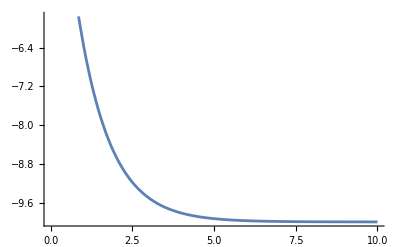

```mathematica
Plot[v[t]/.sol(*veja como substituímos os parâmetros*)/.{g-> 10,b-> 1},{t,0,10}]
```

Para determinarmos a altura da partícula como função do tempo, temos que resolver uma equação diferencial de segunda ordem:

```mathematica
DSolve[y''[t]==-g-b*y'[t],y[t],t]
```

{{y[t]→-(g t)/b-(ⅇ^(-b t) C[1])/b+C[2]}}

Note agora a presença de duas constantes de integração C[1] e C[2], que não estariam presentes se estabelecêssemos as condições iniciais para a velocidade e a altura da partícula:

```mathematica
soly=DSolve[{y''[t]==-g-b*y'[t],y'[0]==0,y[0]==h},y[t],t]//Simplify
```

{{y[t]→(g-ⅇ^(-b t) g+b^2 h-b g t)/b^2}}

Traçando o gráfico de y(t), notamos mais uma vez o efeito da velocidade terminal:

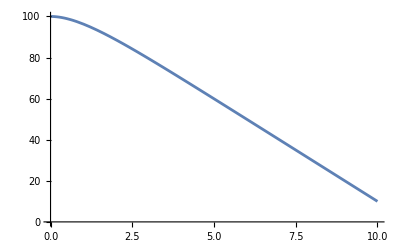

```mathematica
Plot[y[t]/.soly/.{g-> 10,b-> 1,h-> 100},{t,0,10}]
```

Também é possível utilizar a solução para definir uma função do tempo a ser manipulada em outros cálculos. Para isso, é preciso “eliminar” as chaves na solução, o que pode ser feito com a sintaxe abaixo:

```mathematica
altura[t_]:=y[t]/.soly[[1]] (*Também poderíamos eliminar a chave com Flatten*)
```

Temos que dar para a função um nome diferente de y[t_] para evitar problemas com uma definição recursiva.

```mathematica
altura[t]
```

Com essa definição, fica mais fácil efetuar cálculos. Por exemplo, podemos investigar o limite do resultado quando a resistência do ar se torna desprezível, utilizando a função Limit:

```mathematica
Limit[altura[t],b-> 0]
```

Note que teríamos problemas se tentássemos calcular essa mesma função utilizando o operador de substituição:

```mathematica
altura[t]/.b-> 0
```

Power::infy: Infinite expression 1/0^2 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Indeterminate

A função DSolve também lida com sistemas de equações diferenciais ordinárias acopladas. Vamos ilustrar essa capacidade com o problema de duas partículas conectadas a molas, conforme mostrado na figura abaixo.

As equações de movimento são as seguintes:

Introduzindo  e supondo que o sistema seja abandonado do repouso, apenas com a massa da esquerda deslocada de uma quantidade , temos

```mathematica
(*Defina primeiro as equações separadamente para o código ficar mais legível*)
```

```mathematica
eq1=x1''[t]==-ω^2*(2*x1[t]-x2[t]); 
eq2=x2''[t]==-ω^2*(2*x2[t]-x1[t]);
```

```mathematica
sol12=DSolve[{eq1,eq2,x1[0]==A,x2[0]==0,x1'[0]==0,x2'[0]==0},{x1[t],x2[t]},t]//FullSimplify
```

{{x1[t]→1/2 A (Cos[t ω]+Cos[√3 t ω]),x2[t]→1/2 A (Cos[t ω]-Cos[√3 t ω])}}

Se quisermos definir funções para as soluções, temos que nos referir às regras de transformação separadamente, o que pode ser feito com o auxílio da função Part da seguinte forma:

```mathematica
sol12[[1,1]] 
sol12[[1,2]]
```

x1[t]→1/2 A (Cos[t ω]+Cos[√3 t ω])

x2[t]→1/2 A (Cos[t ω]-Cos[√3 t ω])

Logo, vamos definir

```mathematica
pos1[t_]:=x1[t]/.sol12[[1,1]]
pos2[t_]:=x2[t]/.sol12[[1,2]]
```

Vamos fazer gráficos das soluções, supondo ω=2π e A=5 (em unidades arbitrárias):

```mathematica
(*É sempre interessante guardar todas as variáveis de interesse em uma lista subs ou pars*)
```

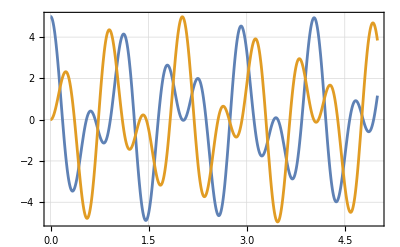

```mathematica
subs={ω-> 2*π,A-> 5};
Plot[{pos1[t]/.subs,pos2[t]/.subs},{t,0,5}, GridLines->Automatic,Frame->True]
```

Note que as soluções são superposições de movimentos harmônicos com duas frequências distintas, ω e √3 ω. Esses são os chamados modos normais de oscilação do sistema, e correspondem a situações em que as duas massas movem-se com a mesma frequência e com uma fase relativa fixa. Por simetria, essas situações devem corresponder a abandonar o sistema do repouso com (i) x_1=x_2 ou (ii) x_1=-x_2, o que pode ser confirmado pela solução explícita das equações de movimento:

```mathematica
DSolve[{eq1,eq2,x1[0]==A,x2[0]==A,x1'[0]==0,x2'[0]==0},{x1[t],x2[t]},t]//FullSimplify (* Primeiro modo normal *)
```

{{x1[t]→A Cos[t ω],x2[t]→A Cos[t ω]}}

```mathematica
DSolve[{eq1,eq2,x1[0]==A,x2[0]==-A,x1'[0]==0,x2'[0]==0},{x1[t],x2[t]},t]//FullSimplify (* Segundo modo normal *)
```

{{x1[t]→A Cos[√3 t ω],x2[t]→-A Cos[√3 t ω]}}

Equações diferenciais que não podem ser resolvidas analiticamente requerem o uso da função NDSolve, cuja sintaxe vamos exemplificar a seguir.

Considere primeiro um pêndulo simples, de comprimento L, mas não restrito ao limite de pequenas oscilações. Nesse caso, a equação de movimento para o ângulo θ de desvio em relação à vertical é θ^(..)=-ω^2senθ, com ω=√(g/L), que não admite solução analítica fechada. A solução numérica, supondo ω=2π rad e um pêndulo partindo do repouso, com um ângulo θ_0=π/3 rad, é obtida entre t=0 e t=10 s pela sintaxe abaixo:

```mathematica
sol=NDSolve[{θ''[t]==-ω^2*Sin[θ[t]],θ'[0]==0,θ[0]==θ0}/.{ω-> 2*π,θ0-> π/3},θ,{t,0,10}] (*A diferença está no fato de que a variável independente fica em um intervalo*)
```

{{θ→InterpolatingFunction[…]}}

Note que o Mathematica retorna uma solução em forma de uma “função de interpolação”, que permite obter uma estimativa para a solução em qualquer ponto do intervalo entre t=0 e t=10 s. (A “interpolação” vem do fato de que a solução numérica é obtida estritamente para um conjunto discreto de pontos, fora dos quais há um ajuste, geralmente polinomial, para fornecer novas estimativas.)

Assim como antes, podemos definir uma função a partir da solução:

```mathematica
angulo[t_]:=θ[t]/.sol[[1]]
```

Vamos produzir um gráfico do ângulo como função do tempo, colocando também o comportamento harmônico caso valesse o limite de pequenas oscilações:

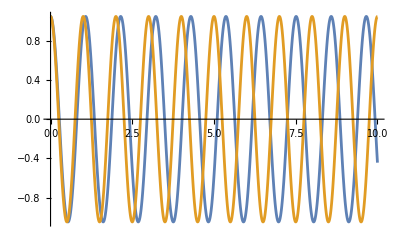

```mathematica
Plot[{angulo[t],π/3*Cos[2*π*t]},{t,0,10}]
```

Vemos claramente que o período “verdadeiro” é maior do que aquele previsto pela aproximação de pequenas oscilações. Essa tendência se acentua à medida que o ângulo inicial aumenta:

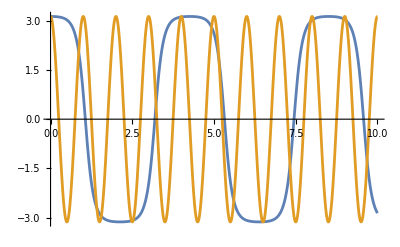

```mathematica
subs={ω-> 2*π,θ0-> π-0.01}; 
sol=NDSolve[{θ''[t]==-ω^2*Sin[θ[t]],θ'[0]==0,θ[0]==θ0}/.subs,θ,{t,0,10}] ;
Plot[{angulo[t],θ0*Cos[ω*t]/.subs},{t,0,10}]
```

Note que, como definimos a função angulo[t] com atribuição retardada, não precisamos redefini-la quando atualizamos a variável sol.

## Exercícios no E-disciplinas

Também estará disponível, uma hora após o final da aula, a primeira lista de exercícios, que deve ser entregue até uma hora antes do início da aula do dia 26 de setembro.